```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/johannesk/kette_repo/limit_cycles/src_mathematica/Ganesh

```mathematica
hbar=197.327053;
Mm=938.858;
m1=2 Mm;m2=2 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
Print["ℏ^2/(2  μ) = ",1/mh2]
```

ℏ^2/(2  μ) = 20.7369

Read LEC list (e.g. fitted to two-body scattering length via <<<Fit_Scattering_length.nb>>>)

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
(*LECsNUCL=Import["../LECs_nucl_Rimas-Martin.dat","Table"];
activeLEC=LECsNUCL[[All,{1,2}]][[2;;]];*)
activeLEC=Import["./LECs_05MeV.dat","Table"];
```

Calculate the dimer wave function in a Gaussian basis rdimer=∑_(i=1)^N c_i·e^(-α_i r^2)

```mathematica
I1=Compile[{lam,b1,b2},(Pi/(2b1+2b2+lam^2))^(3/2)];
I3=Compile[{b1,b2},3 b1 b2 Pi^(3/2)/(2^(1/2)(b1+b2)^(5/2))];
```

```mathematica
ham=Compile[{lam,b1,b2,lec},Module[{locall=lam},lec I1[lam,b1,b2]+(1/mh2) I3[b1,b2]]];
norm=Compile[{b1,b2},Module[{},(Pi/(2 b1+2 b2))^(3/2)]];
```

```mathematica
ApproxDimerWF[lamd_,dimD_,nbrThreads_,nbrWidthSamples_,minW_,maxW_,minWidthDiff_,verbosity_]:=Block[{LECc,e0,λ=lamd,Δ=minWidthDiff,αmax=maxW,αmin=minW,Nd=dimD,Ns=nbrWidthSamples,Nth=nbrThreads},

LECc=Flatten[Select[activeLEC,#[[1]]==λ&]][[2]];
Print[LECc];
widths={};
rndPrec=5;
Do[
widthLr=Sort[#]&/@RandomReal[{SetPrecision[αmin,rndPrec+1],SetPrecision[αmax,rndPrec+1]},{Ns,Nd},WorkingPrecision->rndPrec];
widthL=Select[widthLr,AllTrue[Select[Tuples[#,2],#[[1]]!=#[[2]]&],Abs[#[[1]]-#[[2]]]>Δ&]&];
AppendTo[widths,widthL];
,{nn,Nth}];

If[verbosity==1,Print["λ = ",λ,"   C_0(λ) = ",LECc,"  #(width-set candidates) = ",Length[Flatten[widths,1]],"  in ",Nth," parallel threads."]];
opti={};
SetSharedVariable[opti];

ta=AbsoluteTime[];
ParallelDo[
widthL=widths[[nt]];
results=0.0;e0=0.0;
optSet={};
Do[
Nd=Length[wi];
hamm=Table[ham[2 λ^0.5,wi[[i]],wi[[j]],LECc],{i,Nd},{j,Nd}];
normm=Table[norm[wi[[i]],wi[[j]]],{i,Nd},{j,Nd}];

{eval,evec}=Eigensystem[{hamm,normm}];

ord=Ordering[Re[eval]];
eigsorted=Re[eval[[ord]]];
vecsorted=evec[[ord]];

If[((eigsorted[[1]]<results)&&(eigsorted[[1]]>-2.5)&&(Im[eigsorted[[1]]]==0)),
(*Print[eigsorted[[1]],eigsorted];*)
e0=eigsorted[[1]];
results=eigsorted[[1]];
optSet=Transpose[{vecsorted[[1]],wi}];
]
,{wi,widthL}];
If[verbosity==1,Print["Core ",nt," : ",e0,optSet]];
AppendTo[opti,{e0,optSet}];
,{nt,Nth}];
tb=AbsoluteTime[];

e0=Sort[opti][[1]][[1]];
optSet=Sort[opti][[1]][[2]];
If[verbosity==1,Print["optimum of ",Style[Length[Flatten[widths,1]],Red,Italic,18]," candidate width sets found in Δt = ",Style[tb-ta,Red,Italic,18]," sec.          : E_0 = ",e0]];
(*Print["opt. basis: ",optSet];*)
(*Put[optSet,"dimerWF_"<>ToString[e0]<>".mmo"];
Put[e0,"E0_"<>ToString[e0]<>".mmo"];*)
{e0,optSet}
];
rma=2;rmi=0.;nR=100;
rR=Range[rmi,rma,(rma-rmi)/nR];
```

-474.27

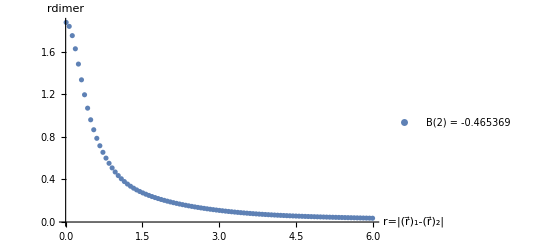

```mathematica
lambdaTest=4;
{eDi,wDi}=ApproxDimerWF[lambdaTest,5,8,10000,0.001,12,0.1,0];

JacobiTrailWavefunctionU=Total[#[[1]] Exp[-#[[2]] r1^2]&/@wDi];
JacobiTrailWavefunctionDataU=Table[JacobiTrailWavefunctionU/.{r1->R1},{R1,rR}];

plotData=Transpose[{rR,JacobiTrailWavefunctionDataU}];
ListPlot[plotData,PlotRange->Full,AxesLabel->{"r=|(r⃗)_1-(r⃗)_2|","rdimer"},PlotLegends->{"B(2) = "<>ToString[eDi]}]
```

```mathematica
RiccatiBesselJ=Compile[{z,l},z SphericalBesselJ[l,z]];
RiccatiBesselN=Compile[{z,l},(-1)^l z SphericalBesselY[l,z]];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha=Compile[{ra,ka,la,ha},RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]];

beta=Compile[{rb,kb,lb,hb},RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])];
```

reference: J. Spanier, K.B. Oldham - An Atlas of Functions (1987)

x·j_n(x)=√((π x)/2)J_(n+1/2)(x)=^(x∈C)√((π x)/2)i^(n+1/2) I_(n+1/2)(Re[x])
with
 j_n: spherical Bessel (1st kind)
 J_n: Bessel (1st kind)
 I_n: modified Bessel (1st kind)
 to optimize runtime, we substitute in this implementation -- valid for S-wave scattering, only:
 j_0(i x)=Sinh[x]/x
 and
 j_1(i x)=i x^-1(Cosh[x]-Sinh[x]/x)
 For numerical stability at arguments x>>1, it is curucial to subsitute the following representation:
 e^(-aR^2-bR'^2) Sinh[bRR']=1/2(e^(-aR^2-bR'^2+bRR')-e^(-aR^2-bR'^2-bRR')) and similarly for the hyperbolic cosine;
 Retaining the Sinh built-in function throws, at best, warnings, and yields significantly inaccurate and almost certainly non-sensical results!

```mathematica
NormTF=Compile[{{core,_Real,2}},Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]]core[[k]][[1]]core[[l]][[1]] (Pi^2/(4 (core[[i]][[2]]+core[[j]][[2]])(core[[k]][[2]]+core[[l]][[2]])))^(3/2),{i,Length[core]},{j,Length[core]},{k,Length[core]},{l,Length[core]}]]]];

VlocTF=Compile[{r,lam,Cc,Dd,Aa,Bb,Gg,Hh},Block[{eta2,eta3,w2,w3},
eta2= (8/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 Cc/(4((1/4)lam^2 Bb + Aa((1/4)lam^2 + 2Gg +2  Bb) + (1/4)lam^2Hh +2 Bb Hh+Gg((1/4)lam^2 +2Hh))^(3/2));
w2= 2(1/4)lam^2(Aa+Hh)(Gg+Bb)/((1/4)lam^2 Bb + Aa((1/4)lam^2+2 Gg+2Bb)+(1/4)lam^2 Hh +2 Bb Hh+Gg((1/4)lam^2+2Hh));
eta3 =(8/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 Cc/(4((1/4)lam^2 Bb + Gg((1/4)lam^2 + 2Bb)+(1/4)lam^2Hh +2Bb Hh + Aa((1/4)lam^2+2Gg+2Hh))^(3/2));
w3 = 2(1/4)lam^2(Aa+Bb)(Gg+Hh)/((1/4)lam^2 Bb + Gg((1/4)lam^2+2Bb)+(1/4)lam^2 Hh +2Bb Hh+Aa((1/4)lam^2+2Gg+2Hh));
eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]
]];

WnolocTF3=Compile[{r,rp,Ee,lam,Cc,Dd,Aa,Bb,Gg,Hh,Ll,TwoMyOverHBsq},Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5/(2(Aa+Bb+Gg+ Hh))^(3/2) (1/TwoMyOverHBsq);
a1=(4Bb Hh + Gg Bb+Gg Hh+Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
b1=(2Gg Bb -2Gg Hh -2 Aa Bb +2 Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
c1=(Gg Bb +Hh Gg+4Aa Gg +Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);

zeta2=-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 Cc/(2(2(1/4)lam^2+Aa +Bb+ Gg+Hh))^(3/2);
zeta3=-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 Cc/(2(2(1/4)lam^2+Aa +Bb+ Gg+Hh))^(3/2);

a2=(4Hh(2(1/4)lam^2+Bb)+Gg(2(1/4)lam^2 +Bb+Hh)+Aa(2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
b2=(Gg(4 (1./4) lam^2+2 Bb-2 Hh)+Aa (-4 (1/4) lam^2-2 Bb+2 Hh))/(2 (2 (1/4) lam^2+Aa+Bb+Gg+Hh));
c2=( Gg(2(1/4)lam^2+Bb+Hh)+Aa(2(1/4)lam^2+4Gg+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));

a3= (4Bb(2(1/4)lam^2+Hh)+Gg(Bb+2(1/4)lam^2+Hh)+Aa(2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
b3=(Gg(2Bb-4(1/4)lam^2-2Hh)+Aa(4(1/4)lam^2+2Hh-2Bb))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
c3=(Gg(Bb+2(1/4)lam^2+Hh)+Aa(4Gg+2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));

Sinh1=(Exp[b1 r rp-a1 r^2-c1 rp^2]-Exp[-b1 r rp-a1 r^2-c1 rp^2])/(2 b1+100 $MachineEpsilon);
Sinh2=(Exp[b2 r rp-a2 r^2-c2 rp^2]-Exp[-b2 r rp-a2 r^2-c2 rp^2])/(2 b2+100 $MachineEpsilon);
Sinh3=(Exp[b3 r rp-a3 r^2-c3 rp^2]-Exp[-b3 r rp-a3 r^2-c3 rp^2])/(2 b3+100 $MachineEpsilon);

-(4 Pi) (zeta1 ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)- TwoMyOverHBsq Ee) Sinh1-4 a1 Sqrt[3]^-1 (-0.5 r rp (Exp[b1 r rp-a1 r^2-c1 rp^2]+Exp[-b1 r rp-a1 r^2-c1 rp^2])+Sinh1))+zeta2 Sinh2+zeta3 Sinh3)
]];
```

```mathematica
SolveSecularP3[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},
t1=AbsoluteTime[];
hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=1/NormTF[a00];

(*Wmat=ConstantArray[0,{Npoints,Npoints}];*)

Wmats={};
SetSharedVariable[Wmats];

Do[

cij=a00[[ii]][[1]] a00[[jj]][[1]] a00[[kk]][[1]]  a00[[ll]][[1]]  normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]]],{i,1,Npoints}]];

wmat=ParallelTable[-hDif^3 TwoMyOverHBsq WnolocTF3[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints},ProgressReporting->False]; 

AppendTo[Wmats,cij (amat+wmat)];

,{ii,1,Length[a00]},{jj,1,Length[a00]},{kk,1,Length[a00]},{ll,1,Length[a00]}];

Wmat=Total[Wmats];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum  Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);
t2=AbsoluteTime[];
Print["finite-difference runtime Δt = ",(t2-t1)/60.," mins"];
tanDelta
];
```

```mathematica
GetEREP3[l_,rMax_,nPoints_,core_,LECc_,energ_:0.001]:=Module[{locall=l},
LECd=0.0;
momFM=Sqrt[mh2 energ];
TanDelSwave=SolveSecularP3[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2];
-Re[TanDelSwave]/Sqrt[mh2 energ ]
]
```

## statistical analysis of the numerical stability of a_dd predictions

Obtain an ensemble of core wave fcuntions

-474.27

Core 1) {-0.426063,{{-0.0938811,0.025687},{-0.30566,0.29323},{-0.636445,1.8141},{-0.701923,7.8013}}}

-474.27

Core 2) {-0.517731,{{0.0441915,0.017096},{0.136386,0.12276},{0.296719,0.65206},{0.659973,3.1931},{-0.315188,5.859},{0.597073,8.2415}}}

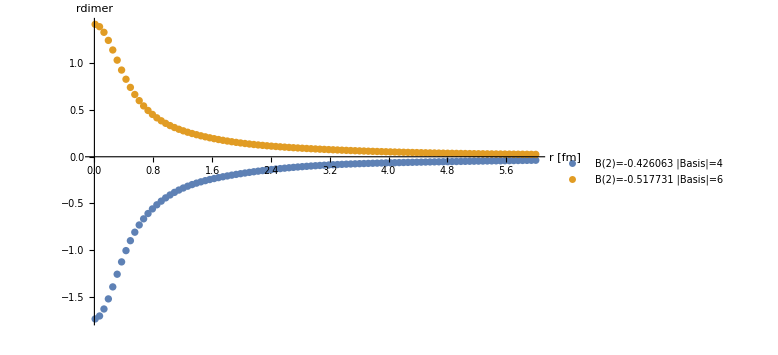

```mathematica
lambdaTest=4;(* 6 10 14 18 *)
nbrOfCores=2;
rndDim=RandomInteger[{4,6},nbrOfCores];
rndUplim=RandomReal[{12,13},nbrOfCores];
dCores={};pltDat={};pltLabs={};
Do[
tmp=ApproxDimerWF[lambdaTest,rndDim[[nn]],8,50000,0.0001,rndUplim[[nn]],0.1,0];

(* only allow those wave functions whith all basis-expansion coefficients larger than a numerical zero *)
If[AllTrue[Abs[tmp[[2]][[All,1]]],#>10^(-10.)&],
AppendTo[dCores,tmp];
Print["Core ",nn,") ",tmp];
JacobiTrailWavefunctionU=Total[#[[1]] Exp[-#[[2]] r1^2]&/@tmp[[2]]];
JacobiTrailWavefunctionDataU=Table[JacobiTrailWavefunctionU/.{r1->R1},{R1,rR}];
plotData=Transpose[{rR,JacobiTrailWavefunctionDataU}];
AppendTo[pltDat,plotData];
AppendTo[pltLabs,{tmp[[1]],rndDim[[nn]]}];
];
,{nn,nbrOfCores}]
Put[dCores,"dimerCores_"<>ToString[lambdaTest]<>".dat"];
ListPlot[#&/@pltDat,PlotRange->Full,AxesLabel->{"r [fm]","rdimer"},PlotLegends->{"B(2)="<>ToString[#[[1]]]<>"  |Basis|="<>ToString[#[[2]]]&/@pltLabs},ImageSize->Large]
```

Obtain dimer-dimer scattering length for the core ensemble

```mathematica
(* energy at which the scattering length is obtained from the amplitude *)
energ=0.01;
(* Integration grid *)
rMa=3.5;
grdPerFermi=35;
nGrd=IntegerPart[rMa grdPerFermi];
results={};
dCores=Get["dimerCores_"<>ToString[lambdaTest]<>".dat"];
nbrOfCores=Length[dCores];
Do[
{e0Core,dimerCore}=dCores[[nn]];

dimCore=Length[dimerCore];

LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]];
tmp=GetEREP3[2 lambdaTest^0.5,rMa,nGrd,dimerCore,LECc,energ];
AppendTo[results,{lambdaTest,LECc,rMa,nGrd,e0Core,dimCore,tmp,tmp/(hbar/√(Mm Abs[e0Core]))}];
Print[nn,")  ",lambdaTest," ",LECc," ",rMa," ",nGrd," ",energ," ",e0Core," ",dimCore," ",tmp,"  ",tmp/(hbar/√(Mm Abs[e0Core]))];
,{nn,nbrOfCores}];
Put[results,"results_aDD_"<>ToString[lambdaTest]<>".res"];
```

finite-difference runtime Δt = 0.967297 mins

1)  4 -474.27 3.5 122 0.01 -0.426063 4 3.66593  0.371564

finite-difference runtime Δt = 5.2501 mins

2)  4 -474.27 3.5 122 0.01 -0.517731 6 7.83421  0.875307

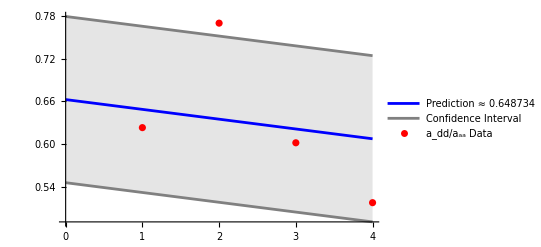

```mathematica
lambdaTest=18;
dCores=Get["dimerCores_"<>ToString[lambdaTest]<>".dat"];
ergebnisse=Get["results_aDD_"<>ToString[lambdaTest]<>".res"];nbrOfCores=Length[dCores];
data=Table[x->ergebnisse[[All,8]][[x]],{x,Range[Length[ergebnisse[[All,8]]]]}];
p=Predict[data,Method->"LinearRegression"];
Information[p];
Show[Plot[{
p[x],
p[x]+StandardDeviation[p[x,"Distribution"]],p[x]-StandardDeviation[p[x,"Distribution"]]},
{x,0,nbrOfCores},
PlotRange->{All,All},
PlotStyle->{Blue,Gray,Gray},
Filling->{2->{3}},
Exclusions->False,
PerformanceGoal->"Speed",PlotLegends->{"Prediction ≈ "<>ToString[p[1]],"Confidence Interval"}
],
ListPlot[List@@@data,PlotStyle->Red,PlotLegends->{"a_dd/a_aa Data"},AxesLabel->{"variational basis","a_dd/a_aa"}]
]
```

EFT parameters | Numerical parameters | plot control
cutoff regulator λ = 6 | R_max = 6 | #(plot grid points) = 100
C_0(λ) = -703.026 | #(Integration grid points) = 30 | plot threshold =  1.
B(2) = -0.499909 | dimer-basis dimension = 6 |

finite-difference runtime Δt = 0.889636 mins

Results | 
a_dd = 9.70507 | a_dd/a = 1.06551

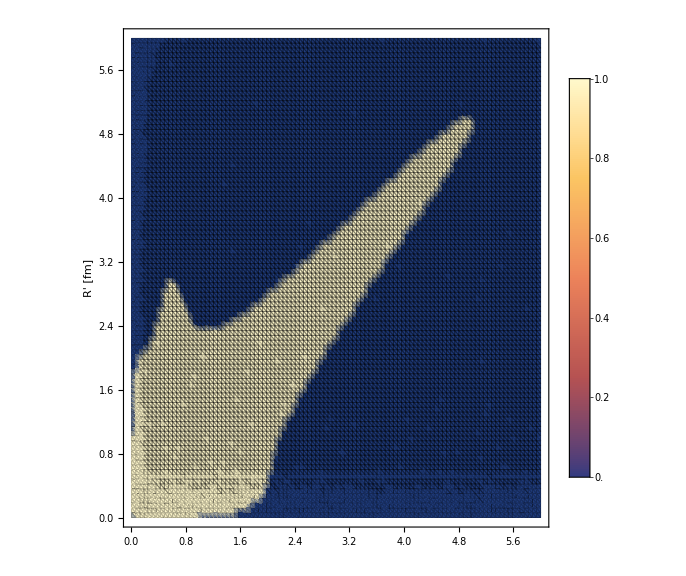
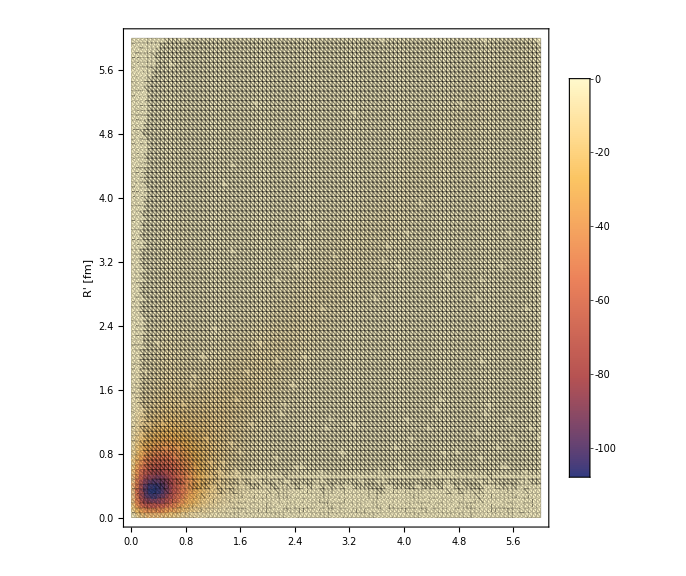
-Graphics- | -Graphics-

```mathematica
dCores=Get["dimerCores_"<>ToString[lambdaTest]<>".dat"];
(* EFT cutoff and energy at which the scattering length is obtained from the amplitude *)
energ=0.01;

(* Integration grid *)
rMa=6;
grdPerFermi=5;
nGrd=IntegerPart[rMa grdPerFermi];

(* Plot parameters for the visualization of V(r,r') *)
nR=100;rMi=0.01;thresh=10^-0;

(* dimer wave-function parameter *)
dimDimer=4;nparallelThreads=8;nDimerWidthSamples=10000;minDimerWidth=0.1;maxDimerWidth=25;midWidthdiff=0.1;

{e0Core,dimerCore}=dCores[[1]];(*ApproxDimerWF[lambd,dimDimer,nparallelThreads,nDimerWidthSamples,minDimerWidth,maxDimerWidth,midWidthdiff,0];*)

normCore=1/NormTF[dimerCore];
dimCore=Length[dimerCore];

LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]];
Grid[{{"EFT parameters","Numerical parameters","plot control"},{"cutoff regulator λ = "<>ToString[lambdaTest],"R_max = "<>ToString[rMa],"#(plot grid points) = "<>ToString[nR]},{"C_0(λ) = "<>ToString[LECc],"#(Integration grid points) = "<>ToString[nGrd],"plot threshold = "NumberForm[N[thresh]]},{"B(2) = "<>ToString[e0Core],"dimer-basis dimension = "<>ToString[dimCore]}},Frame->All]

tmp=GetEREP3[2 lambdaTest^0.5,rMa,nGrd,dimerCore,LECc,energ];
Grid[{{"Results"},{"a_dd = "<>ToString[tmp],"a_dd/a = "<>ToString[tmp/(hbar/√(Mm Abs[e0Core]))]}},Frame->All]

rR=Range[rMi,rMa,(rMa-rMi)/nR];
nR=Length[rR];
potnoloc3d={};
Do[
cij=dimerCore[[ii]][[1]] dimerCore[[jj]][[1]] dimerCore[[kk]][[1]]  dimerCore[[ll]][[1]]  normCore;
potnoloc3dtmp=
Flatten[ParallelTable[{rR[[i]],rR[[j]],mh2 cij WnolocTF3[rR[[i]],rR[[j]],energ,2 lambdaTest^0.5,LECc,0.0,dimerCore[[ii]][[2]],dimerCore[[jj]][[2]],dimerCore[[kk]][[2]],dimerCore[[ll]][[2]],0,mh2]}
,{i,Length[rR]},{j,Length[rR]}],1];
AppendTo[potnoloc3d,potnoloc3dtmp]
,{ii,1,dimCore},{jj,1,dimCore},{kk,1,dimCore},{ll,1,dimCore}]
potnonloc3d=Transpose[{potnoloc3d[[1]][[All,1]],potnoloc3d[[1]][[All,2]],Total[potnoloc3d[[All,All,3]]]}];
chopedMat=ParallelTable[
If[Abs[Re[potnonloc3d[[i]][[3]]]]>=thresh,{potnonloc3d[[i]][[1]],potnonloc3d[[i]][[2]],1},{potnonloc3d[[i]][[1]],potnonloc3d[[i]][[2]],0}]
,{i,Length[potnonloc3d]}];
Grid[{{
ListDensityPlot[chopedMat,Mesh->All,PlotRange->All,PlotLegends->Automatic,ImageSize->Large,Axes->False,Frame->{{True,False},{False,True}},FrameLabel->{{"R' [fm]",None},{None,"R [fm]"}},FrameTicks->All]
,
ListDensityPlot[Re[potnonloc3d],Mesh->All,PlotRange->All,PlotLegends->Automatic,ImageSize->Large,Axes->False,Frame->{{True,False},{False,True}},FrameLabel->{{"R' [fm]",None},{None,"R [fm]"}},FrameTicks->All]
}}]
Put[potnonloc3d,"nonlocPot_"<>ToString[lambdaTest]<>".dat"];
```

### maximal-integration-range dependence of the a_dd scattering-length pre/post-diction

finite-difference runtime Δt = 1.56048 mins

λ = 18   C_0(λ) = -2114.8     R_max = 4.     #(grid points) = 60                a_dd = 3.61559 fm        a_dd/a_aa = 0.702759

finite-difference runtime Δt = 1.87693 mins

λ = 18   C_0(λ) = -2114.8     R_max = 4.4     #(grid points) = 66                a_dd = 3.39436 fm        a_dd/a_aa = 0.65976

finite-difference runtime Δt = 2.13595 mins

λ = 18   C_0(λ) = -2114.8     R_max = 4.8     #(grid points) = 72                a_dd = 3.11869 fm        a_dd/a_aa = 0.606177

finite-difference runtime Δt = 2.37276 mins

λ = 18   C_0(λ) = -2114.8     R_max = 5.2     #(grid points) = 78                a_dd = 3.1492 fm        a_dd/a_aa = 0.612107

finite-difference runtime Δt = 2.87397 mins

λ = 18   C_0(λ) = -2114.8     R_max = 5.6     #(grid points) = 84                a_dd = 3.33224 fm        a_dd/a_aa = 0.647685

finite-difference runtime Δt = 3.10146 mins

λ = 18   C_0(λ) = -2114.8     R_max = 6.     #(grid points) = 90                a_dd = 3.50647 fm        a_dd/a_aa = 0.681551

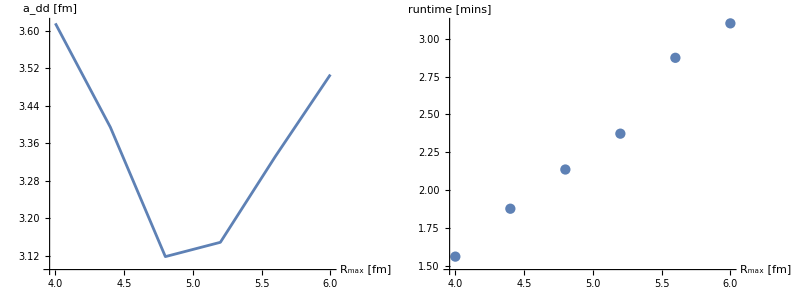

```mathematica
rMaxStart=4.0;
rMaxEnd=6;
nbrR=5;
RmaxRange=Range[rMaxStart,rMaxEnd,N[(rMaxEnd-rMaxStart)/nbrR]];
energ=0.01;
grdPerFermi=15;
results={};
runtimes={};
(*SetSharedVariable[results,resultsPhases];*)
Do[
nGrd=IntegerPart[rMa grdPerFermi];
ta=AbsoluteTime[];
tmp=GetEREP3[lambdaTest,rMa,nGrd,dimerCore,LECc,energ];
tb=AbsoluteTime[];
AppendTo[results,tmp];
AppendTo[runtimes,{rMa,(tb-ta)/60.}];
Print["λ = ",lambdaTest,"   C_0(λ) = ",LECc,"     R_max = ",rMa,"     #(grid points) = ",nGrd,"                a_dd = ",tmp," fm        a_dd/a_aa = ",Style[tmp/(hbar/√(Mm Abs[e0Core])),Red,18]];
,{rMa,RmaxRange}]

Grid[{{ListPlot[Transpose[{RmaxRange,results}],ImageSize->Large,Joined->True,AxesLabel->{"R_max [fm]","a_dd [fm]"}],ListPlot[runtimes,ImageSize->Large,AxesLabel->{"R_max [fm]","runtime [mins]"}]}}]
```

Visualization`Core`ListPlot3D::arrayerr: -- Message text not found -- (Re[4.→0.593595])

Visualization`Core`ListPlot3D::arrayerr: -- Message text not found -- (Re[4.→0.517231])

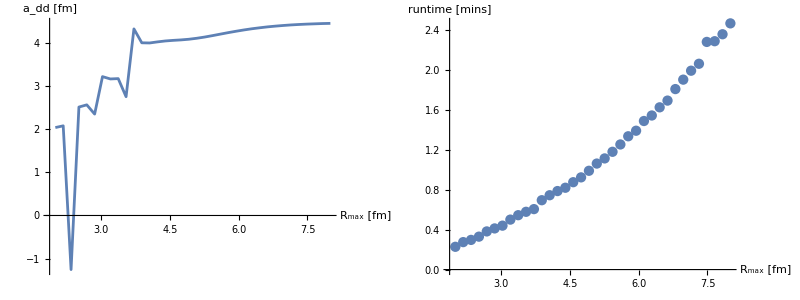

Part::partd: Part specification data⟦4⟧ is longer than depth of object.

Visualization`Core`ListPlot3D::arrayerr: -- Message text not found -- (Re[data⟦4⟧])

```mathematica
lamds={6,10,14,18};
data=Get["nonlocPot_"<>ToString[#]<>".dat"]&/@lamds;
Manipulate[ListPlot3D[Re[data[[n]]],PlotRange->All],{n,Range[1,Length[lamds],1]}]
```

### Grid - density dependence of the a_dd scattering-length pre/post-diction

```mathematica
nGrdi=3;
nGrdiMi=15;
nGrdiMa=252+nGrdiMi;
nGr=Range[nGrdiMi,nGrdiMa,Quotient[nGrdiMa-nGrdiMi,nGrdi]];

results={};
runtimes={};
(*SetSharedVariable[results,resultsPhases];*)
Do[
Print["λ = ",lamd,"   C_0(λ) = ",LECc,"     R_max = ",rMa,"     #(grid points) = ",nGrd];
ta=AbsoluteTime[];
tmp=GetEREP3[lamd,rMa,nGrd,dimerCore,LECc,energ];
tb=AbsoluteTime[];
AppendTo[results,tmp];
AppendTo[runtimes,{nGrd,tb-ta}];
Print["a_dd = ",tmp," fm"];
,{nGrd,nGr}]

Grid[{{ListPlot[Transpose[{nGr,results}],ImageSize->Large,Joined->True,AxesLabel->{"#(grid points)","a_dd [fm]"}],ListPlot[Transpose[{nGr,tt}],ImageSize->Large,AxesLabel->{"#(grid points)","runtime [s]"}]}}]
```

λ = 6   C_0(λ) = -1090.55     R_max = 8     #(grid points) = 15

finite-difference runtime Δt = 0.197998 mins

a_dd = 4.96257 fm

λ = 6   C_0(λ) = -1090.55     R_max = 8     #(grid points) = 99

finite-difference runtime Δt = 1.97576 mins

a_dd = 4.95642 fm

λ = 6   C_0(λ) = -1090.55     R_max = 8     #(grid points) = 183

finite-difference runtime Δt = 6.465 mins

a_dd = 5.05838 fm

λ = 6   C_0(λ) = -1090.55     R_max = 8     #(grid points) = 267

```mathematica
results
aasy=results[[-1]]
Print["a_dd/a =",aasy/(hbar/√(Mm Abs[e0Core]))]
```

{3.92438,3.2987,5.27317,4.55745,4.26782,4.2665,4.40619,4.53118,4.61594,4.6741,4.71599}

4.71599

a_dd/a =0.878303